# Subspace recompilation for BCS Hamiltonian

Set environment, such as threads, gpu, etc.

```mathematica
(*SetEnvironment["OMP_NUM_THREADS"->"8"]*)
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_gpu"];
```

### Modules

```mathematica
GetBlocks::usage="GetBlocks[blockdiagmat_,draw_:True]. Partition indices of a matrix by its blocks.";
GetBlocks[mat_,draw_:True]:=Module[{adjmat,dim=Length@mat,graph},
adjmat=ConstantArray[0,{dim,dim}];
Table[adjmat⟦i,j⟧=If[mat⟦i,j⟧==0,0,1],{i,dim},{j,dim}];
graph=AdjacencyGraph@adjmat;
If[draw,Print@graph];
ConnectedComponents@graph-1
]
```

## BCS simulation

```mathematica
(* non-iteracting harmonic oscillator-type energy levels *)
ϵ=ω(#+0.5)&/@Range[0,4];
(* time-dependent coupling function *)
coupling[t_,g0_,gc_]:=ExpandAll[
(ArcTan[(t-t1)J/(ℏ Γ)]+π/2)(ArcTan[(t2-t)J/(ℏ Γ)]+π/2)(gc-g0)/π^2+g0
]
```

```mathematica
constants={
(* time start to quench and reverse. J is an arbitrary energy unit *)
t1->9 ℏ/J,
t2->18 ℏ/J,
(* initial coupling constant*)
Γ->0.1,
(* frequency *)
ω->5J/3
};
```

```mathematica
(* mean-field eigenvalues *)
Ej[ϵ_,Δ_]:=Sqrt[ϵ^2+Abs[Δ]^2]
(* superconducting gap *)
(*2/g=∑_k 1/Subscript[E, k] tanh[Subscript[E, k]/(2 Subscript[k, b] Temp)]*)
(* since we consider temperature Temp=0, tanh(∞)=1 *)
(* Superconducting gaps*)
Δ0=J;
Δc=2J;
```

```mathematica
g0=2 /Total[1/Ej[ϵ,Δ0]];
gc=2/ Total[1/Ej[ϵ,Δc]];
```

The entire BCS Hamiltonian

```mathematica
Hgaudin[q_,n_,ϵ_,g_]:=Total@Table[({Subscript[X, q],Subscript[Y, q],Subscript[Z, q]}.{Subscript[X, j],Subscript[Y, j],Subscript[Z, j]})/(2(ϵ[[q+1]]-ϵ[[j+1]])), {j,Complement[Range[0,n-1],{q}]}]+Subscript[Z, q]/g
```

```mathematica
HBCS[n_,ϵ_,τ_]:=With[{g=coupling[τ*ℏ/Δ0,g0,gc]/.constants},
SimplifyPaulis@Chop@ExpandAll[
Total@Table[
Simplify[(-g ϵ[[q+1]]+g^2/2)Hgaudin[q,n,ϵ,g]/Δ0/.constants,J>0]
,{q,n-1}]+
SimplifyPaulis@Chop@ExpandAll[SimplifyPaulis@Simplify[g^3/(4Δ0)*(Total@Table[Hgaudin[q,n,ϵ,g],{q,0,n-1}])^2/.constants,J>0]]
]
]
```

Constants

```mathematica
(*mean field-eigenvalues*)
ej=Simplify[Ej[ϵ,Δ0]/.constants,J>0];
(* |Subscript[v, j]|^2, |Subscript[u, j]|^2 *)
ujs=Simplify[0.5(1+ϵ/ej)/.constants,J>0];
vjs=Simplify[0.5(1-ϵ/ej)/.constants,J>0];
```

```mathematica
(*  
Subscript[u, j] 0-Subscript[v, j] 1;
Ry[θ]0=Cos[θ/2]0-Sin[θ/2]1 
 *)
θinit=2*ArcCos@Sqrt@ujs;
```

initial states and memory allocation

```mathematica
DestroyAllQuregs[]
{ψexact,ψinitexact}=CreateQuregs[5,2];
```

```mathematica
(*exact groundstate*)
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

## Obtain the expression ⅇ^(-i δt H_BCS)

```mathematica
(* Medium resolution *)
τs=Sort@DeleteDuplicates@Chop@Join[{0.,4.,8.},Range[8.,20.,0.2],{20.,23.5,27}]
(* the timesteps *)
δτ=Table[τs[[i]]-τs[[i-1]],{i,2,Length@τs}];
PrependTo[δτ,0];
(*sanity check*)
And@@Table[τs[[i]]==Total[δτ[[#]]&/@Range[i]],{i,Length@τs}]
(*τ=t J/ℏ*)
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

True

```mathematica
Length@τs
```

65

The time-dependent gap Δ is controlled through g(t). Definition of g(t) is here

```mathematica
(*τ=t J/ℏ*)
```

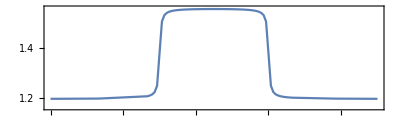

```mathematica
gvals=Simplify[(coupling[#*ℏ/Δ0,g0,gc]/Δ0&/@τs)//.constants,J>0];
ListPlot[Transpose@{τs,gvals},PlotRange->{1.16,1.56},Joined->True,AspectRatio->0.3,Frame->True,FrameTicks->{{Range[1,1.55,0.05],None},{Range[0,27,1],None}}]
```

```mathematica
τs
```

{0,4.,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.,10.2,10.4,10.6,10.8,11.,11.2,11.4,11.6,11.8,12.,12.2,12.4,12.6,12.8,13.,13.2,13.4,13.6,13.8,14.,14.2,14.4,14.6,14.8,15.,15.2,15.4,15.6,15.8,16.,16.2,16.4,16.6,16.8,17.,17.2,17.4,17.6,17.8,18.,18.2,18.4,18.6,18.8,19.,19.2,19.4,19.6,19.8,20.,23.5,27}

```mathematica
τs[[32]]
```

13.8

```mathematica
δτ[[33;;]]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.2,3.5,3.5}

**** Compile @Tue 20 Dec 2022 12:18:23 τ=13.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 12:25:46 completed with ngates=48, cost=0.00001255383112441777, at eval=1652

Cycle 2@Tue 20 Dec 2022 12:29:09 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 12:35:11 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000125538

τ=14.; δ=0.2; cost=0.0000125538; ngates=48; runtime=18.3611 min

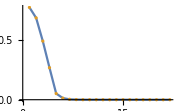

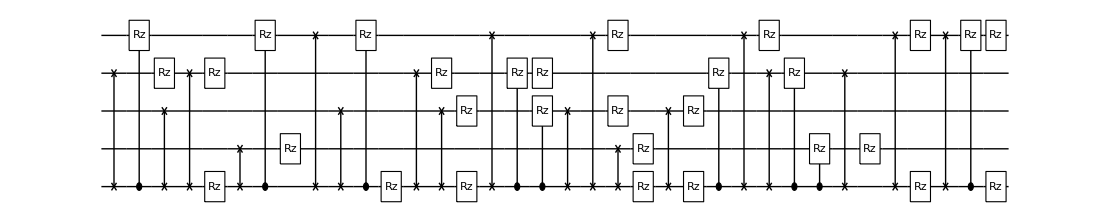

**** Compile @Tue 20 Dec 2022 12:36:45 τ=14.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 12:43:54 completed with ngates=49, cost=7.149820433483001e-6, at eval=1645

Cycle 2@Tue 20 Dec 2022 12:47:06 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 12:53:25 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=7.14982×10^-6

τ=14.2; δ=0.2; cost=7.14982×10^-6; ngates=49; runtime=18.2727 min

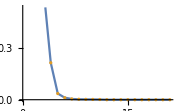

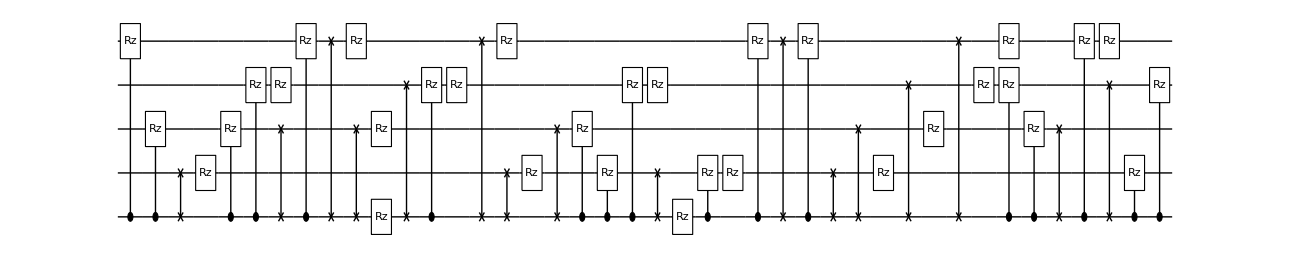

**** Compile @Tue 20 Dec 2022 12:55:01 τ=14.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 13:00:45 completed with ngates=38, cost=0.00001819776638867232, at eval=1580

Cycle 2@Tue 20 Dec 2022 13:03:04 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 13:07:52 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000181978

τ=14.4; δ=0.2; cost=0.0000181978; ngates=38; runtime=13.78 min

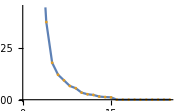

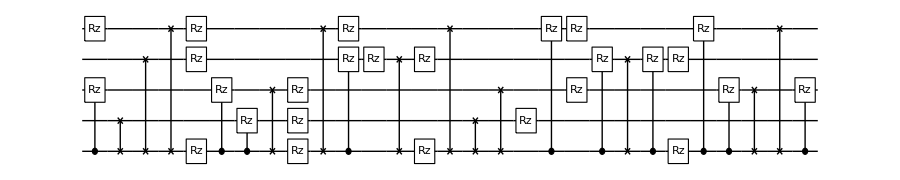

**** Compile @Tue 20 Dec 2022 13:08:48 τ=14.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 13:16:09 completed with ngates=42, cost=0.00014676319683659678, at eval=1580

Cycle 2@Tue 20 Dec 2022 13:22:11 completed with ngates=35, cost=5.892719571964911e-6, at eval=2939

Cycle 3@Tue 20 Dec 2022 13:25:12 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 13:30:53 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=5.89272×10^-6

τ=14.6; δ=0.2; cost=5.89272×10^-6; ngates=35; runtime=26.0649 min

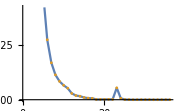

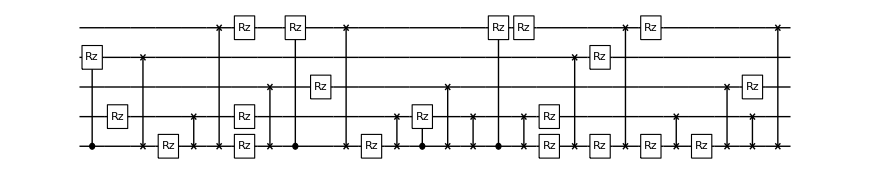

**** Compile @Tue 20 Dec 2022 13:34:52 τ=14.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 13:41:58 completed with ngates=43, cost=0.00007075010537516135, at eval=1703

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

Cycle 2@Tue 20 Dec 2022 13:48:10 completed with ngates=41, cost=9.51281369865331e-6, at eval=3175

Cycle 3@Tue 20 Dec 2022 13:50:48 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 13:56:02 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=9.51281×10^-6

τ=14.8; δ=0.2; cost=6.07905×10^-6; ngates=41; runtime=22.4659 min

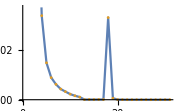

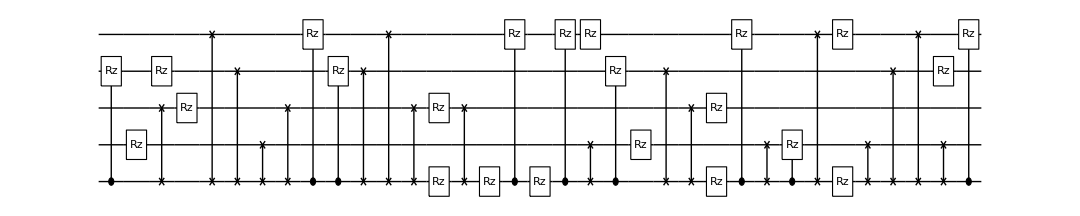

**** Compile @Tue 20 Dec 2022 13:57:22 τ=14.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 14:03:40 completed with ngates=41, cost=0.00001884119956607755, at eval=1678

Cycle 2@Tue 20 Dec 2022 14:11:16 completed with ngates=53, cost=2.0856697456883566e-6, at eval=3358

Cycle 3@Tue 20 Dec 2022 14:14:53 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 14:21:43 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=2.08567×10^-6

τ=15.; δ=0.2; cost=2.08567×10^-6; ngates=53; runtime=26.9745 min

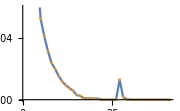

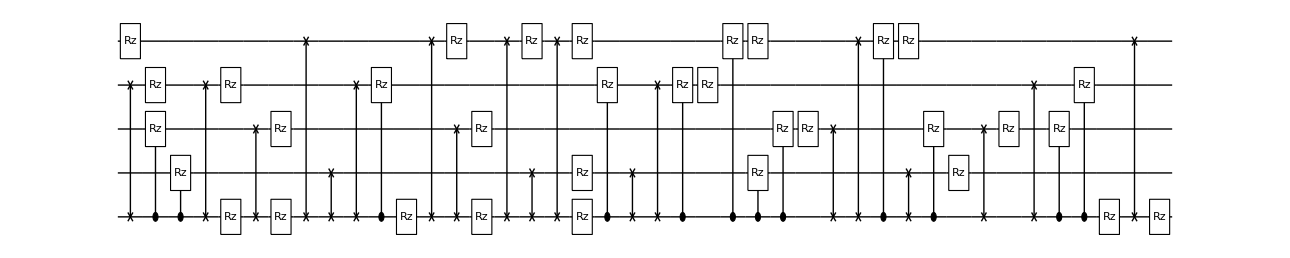

**** Compile @Tue 20 Dec 2022 14:24:21 τ=15.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 14:32:29 completed with ngates=43, cost=0.000015118922436885285, at eval=1993

Cycle 2@Tue 20 Dec 2022 14:35:28 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 14:53:17 completed with ngates=59, cost=7.497005025669523e-7, at eval=4909

τ=15.2; δ=0.2; cost=7.49701×10^-7; ngates=59; runtime=33.2727 min

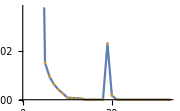

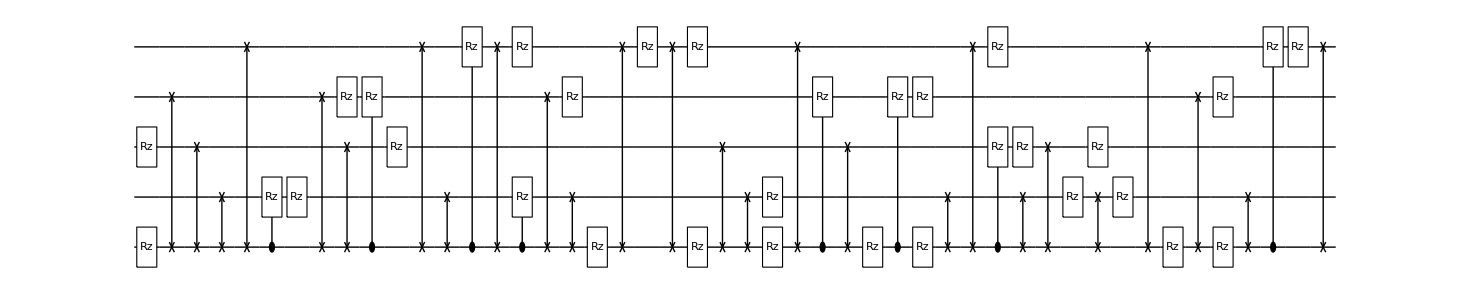

**** Compile @Tue 20 Dec 2022 14:57:37 τ=15.2; δ0.2 ****

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

Cycle 1@Tue 20 Dec 2022 15:03:44 completed with ngates=43, cost=0.00011531232379569101, at eval=1626

Cycle 2@Tue 20 Dec 2022 15:09:13 completed with ngates=29, cost=0.000036949933210461694, at eval=3316

Cycle 3@Tue 20 Dec 2022 15:11:22 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 15:15:40 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000369499

τ=15.4; δ=0.2; cost=0.0000352571; ngates=29; runtime=18.5844 min

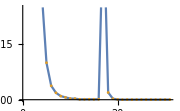

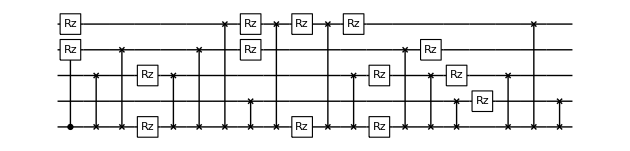

**** Compile @Tue 20 Dec 2022 15:16:12 τ=15.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 15:21:51 completed with ngates=37, cost=0.00011772652891528512, at eval=1479

Cycle 2@Tue 20 Dec 2022 15:27:37 completed with ngates=39, cost=0.00003172157256625674, at eval=2828

Cycle 3@Tue 20 Dec 2022 15:30:34 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 15:43:21 completed with ngates=50, cost=5.959566741431388e-6, at eval=5414

Cycle 5@Tue 20 Dec 2022 15:50:23 adjust hyperparams, slowdown:True

ApplyCircuitDerivs::error: An equal number of variables and ouptut quregs must be passed.

General::stop: Further output of ApplyCircuitDerivs::error will be suppressed during this calculation.

τ=15.6; δ=0.2; cost=4.38804×10^-7; ngates=58; runtime=59.1524 min

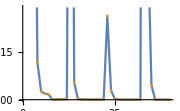

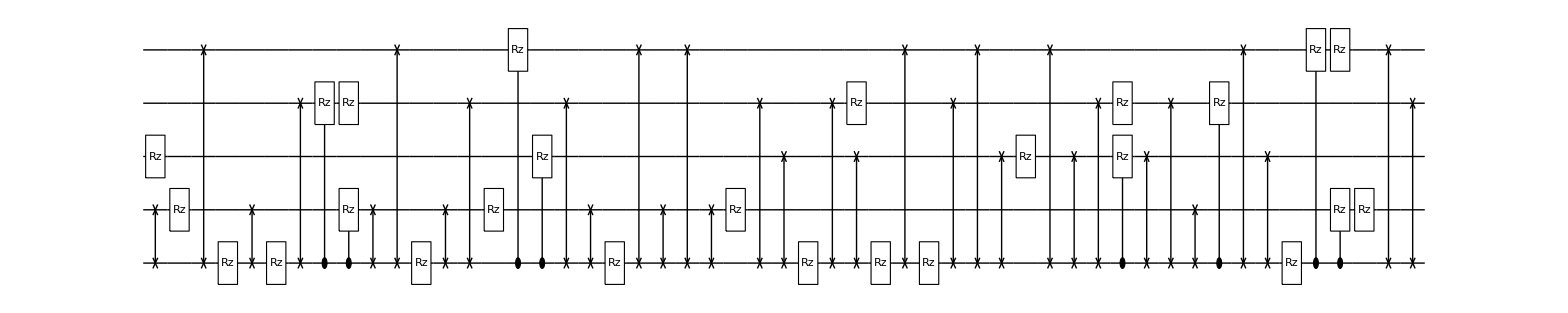

**** Compile @Tue 20 Dec 2022 16:15:22 τ=15.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 16:22:22 completed with ngates=41, cost=0.00008212348885849874, at eval=1614

Cycle 2@Tue 20 Dec 2022 16:29:00 completed with ngates=45, cost=9.444532300451058e-6, at eval=3025

Cycle 3@Tue 20 Dec 2022 16:32:19 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 16:38:17 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=9.44453×10^-6

τ=15.8; δ=0.2; cost=7.90826×10^-6; ngates=45; runtime=24.5932 min

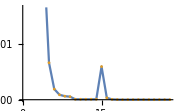

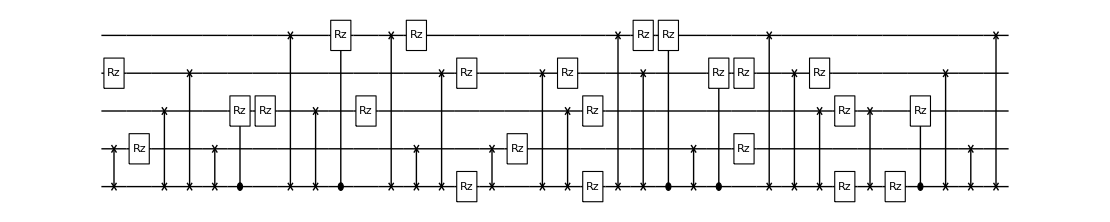

**** Compile @Tue 20 Dec 2022 16:39:57 τ=15.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 16:47:22 completed with ngates=46, cost=0.0000126552392054613, at eval=1705

Cycle 2@Tue 20 Dec 2022 16:54:36 completed with ngates=50, cost=1.70126960596928e-6, at eval=3183

Cycle 3@Tue 20 Dec 2022 16:58:07 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 17:04:47 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=1.70127×10^-6

τ=16.; δ=0.2; cost=1.70127×10^-6; ngates=50; runtime=26.896 min

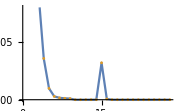

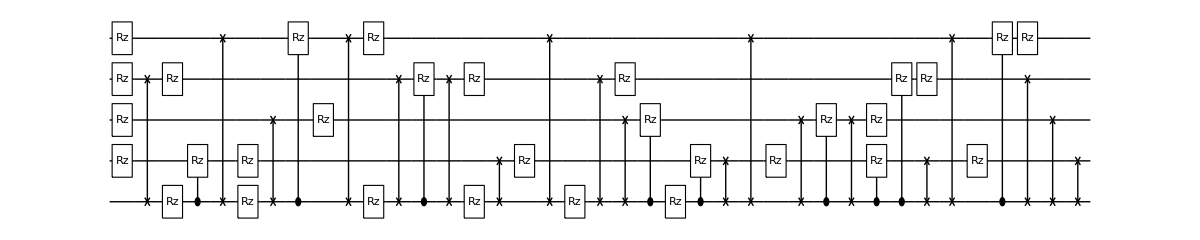

**** Compile @Tue 20 Dec 2022 17:06:51 τ=16.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 17:14:05 completed with ngates=46, cost=0.000010288713498618485, at eval=1669

Cycle 2@Tue 20 Dec 2022 17:17:17 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 17:36:53 completed with ngates=66, cost=1.5530542756270194e-6, at eval=4738

Cycle 4@Tue 20 Dec 2022 17:45:45 adjust hyperparams, slowdown:True

τ=16.2; δ=0.2; cost=6.162×10^-7; ngates=59; runtime=61.8904 min

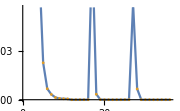

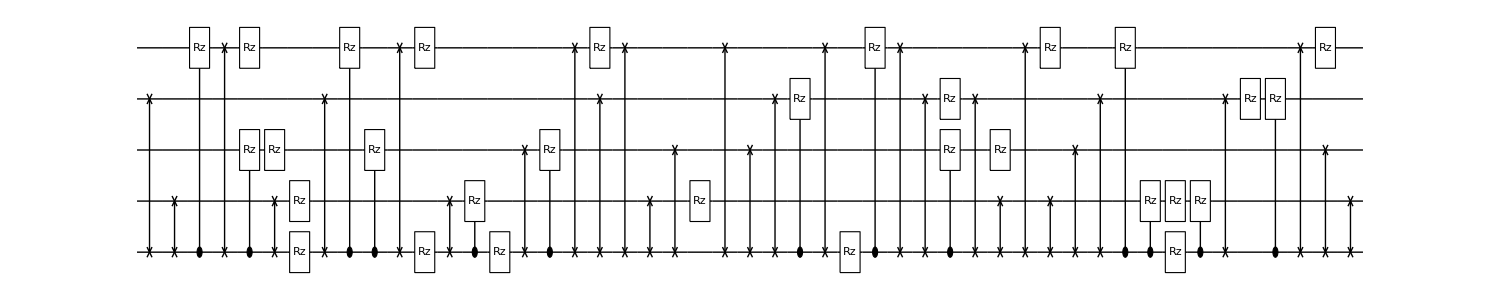

**** Compile @Tue 20 Dec 2022 18:08:45 τ=16.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 18:15:23 completed with ngates=47, cost=0.00001746835112281797, at eval=1646

Cycle 2@Tue 20 Dec 2022 18:18:21 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 18:34:05 completed with ngates=62, cost=4.993283843068852e-6, at eval=4602

Cycle 4@Tue 20 Dec 2022 18:40:59 adjust hyperparams, slowdown:True

τ=16.4; δ=0.2; cost=4.35111×10^-7; ngates=77; runtime=65.8552 min

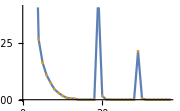

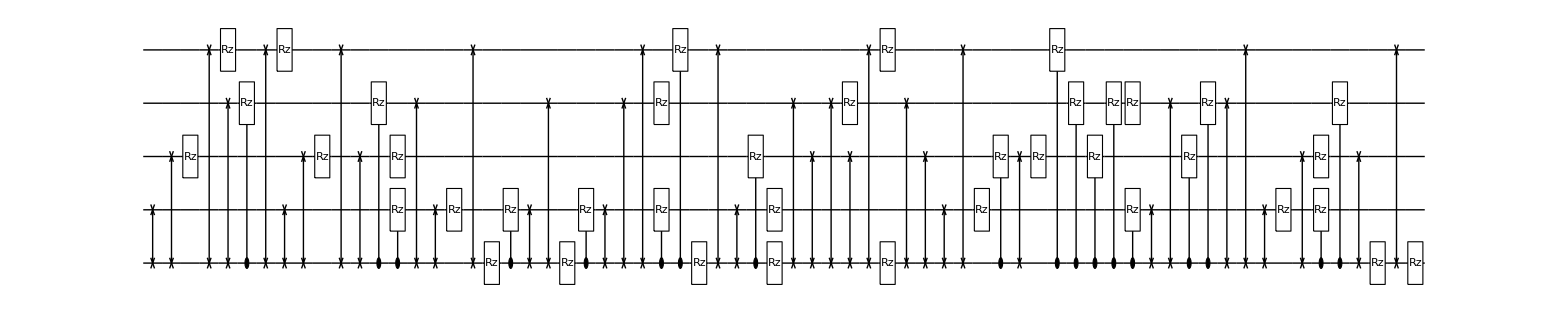

**** Compile @Tue 20 Dec 2022 19:14:37 τ=16.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 19:21:56 completed with ngates=41, cost=0.00002229296667410896, at eval=1684

Cycle 2@Tue 20 Dec 2022 19:30:14 completed with ngates=53, cost=1.9059140103916405e-6, at eval=3220

Cycle 3@Tue 20 Dec 2022 19:34:15 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 19:41:15 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=1.90591×10^-6

τ=16.6; δ=0.2; cost=1.10321×10^-6; ngates=53; runtime=29.0004 min

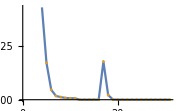

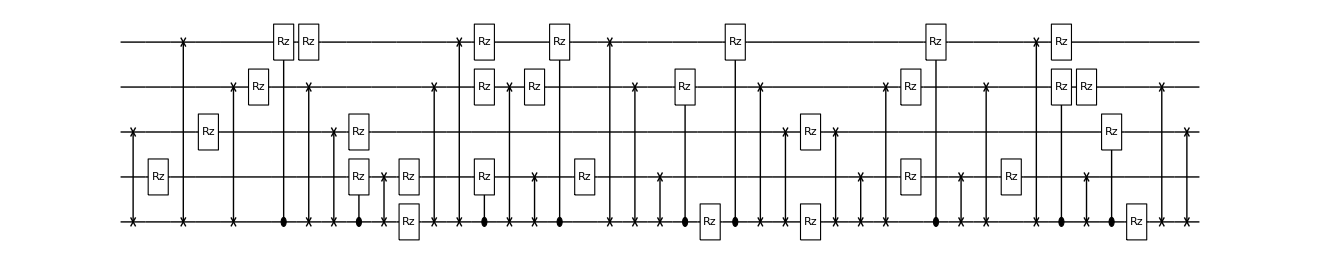

**** Compile @Tue 20 Dec 2022 19:43:37 τ=16.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 19:49:54 completed with ngates=47, cost=0.00011330699488598661, at eval=1565

Cycle 2@Tue 20 Dec 2022 19:58:11 completed with ngates=40, cost=0.000011799854164884493, at eval=3376

Cycle 3@Tue 20 Dec 2022 20:01:14 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 20:07:29 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000117999

τ=16.8; δ=0.2; cost=0.0000106726; ngates=40; runtime=26.7885 min

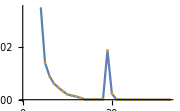

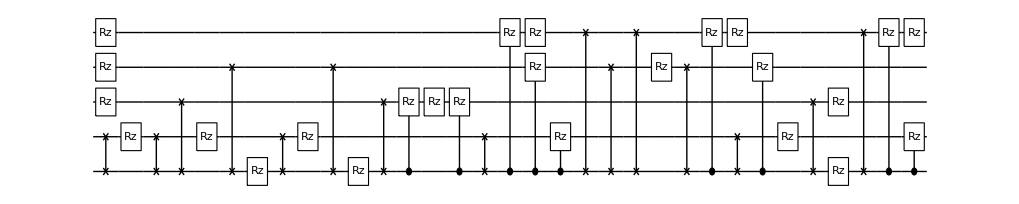

**** Compile @Tue 20 Dec 2022 20:10:24 τ=16.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 20:17:25 completed with ngates=45, cost=2.652215927878565e-6, at eval=1637

Cycle 2@Tue 20 Dec 2022 20:20:28 adjust hyperparams, slowdown:True

τ=17.; δ=0.2; cost=6.19618×10^-7; ngates=57; runtime=30.9106 min

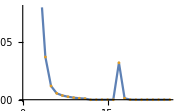

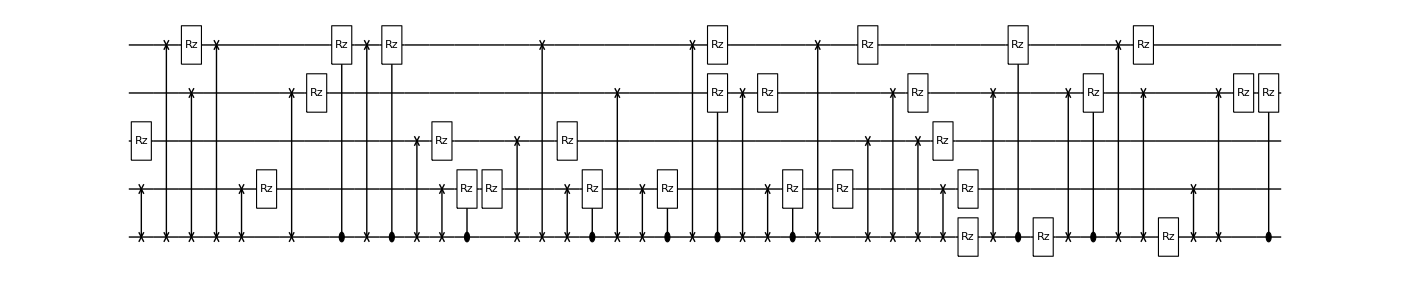

**** Compile @Tue 20 Dec 2022 20:41:19 τ=17.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 20:47:30 completed with ngates=39, cost=0.000015168543862964512, at eval=1512

@cycle2, pathetic result.

Cycle 2@Tue 20 Dec 2022 20:50:32 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 20:55:43 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000141953

τ=17.2; δ=0.2; cost=4.85087×10^-6; ngates=39; runtime=15.3685 min

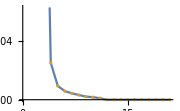

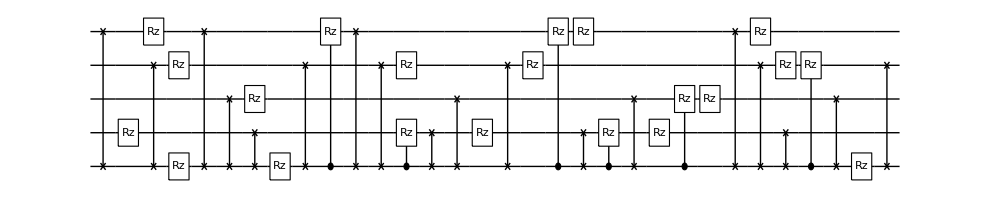

**** Compile @Tue 20 Dec 2022 20:56:48 τ=17.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 21:02:38 completed with ngates=39, cost=0.000032178410574235095, at eval=1540

Cycle 2@Tue 20 Dec 2022 21:08:48 completed with ngates=51, cost=0.000012138554806639945, at eval=3016

Cycle 3@Tue 20 Dec 2022 21:12:22 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 21:31:36 completed with ngates=62, cost=8.390439621974721e-7, at eval=6029

τ=17.4; δ=0.2; cost=8.39044×10^-7; ngates=62; runtime=38.1615 min

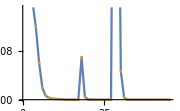

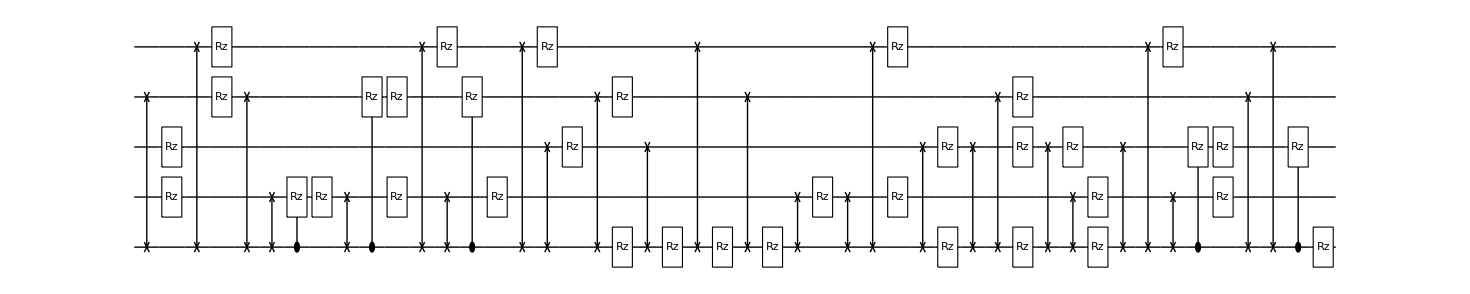

**** Compile @Tue 20 Dec 2022 21:35:04 τ=17.4; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 21:43:04 completed with ngates=41, cost=0.0000411489573697299, at eval=1982

Cycle 2@Tue 20 Dec 2022 21:49:27 completed with ngates=45, cost=9.397032525781945e-6, at eval=3465

Cycle 3@Tue 20 Dec 2022 21:59:07 completed with ngates=61, cost=1.7177975264459633e-6, at eval=5072

Cycle 4@Tue 20 Dec 2022 22:03:36 adjust hyperparams, slowdown:True

@cycle5, pathetic result.

Cycle 5@Tue 20 Dec 2022 22:11:47 adjust hyperparams, slowdown:True

τ=17.6; δ=0.2; cost=9.79413×10^-7; ngates=59; runtime=42.4038 min

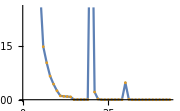

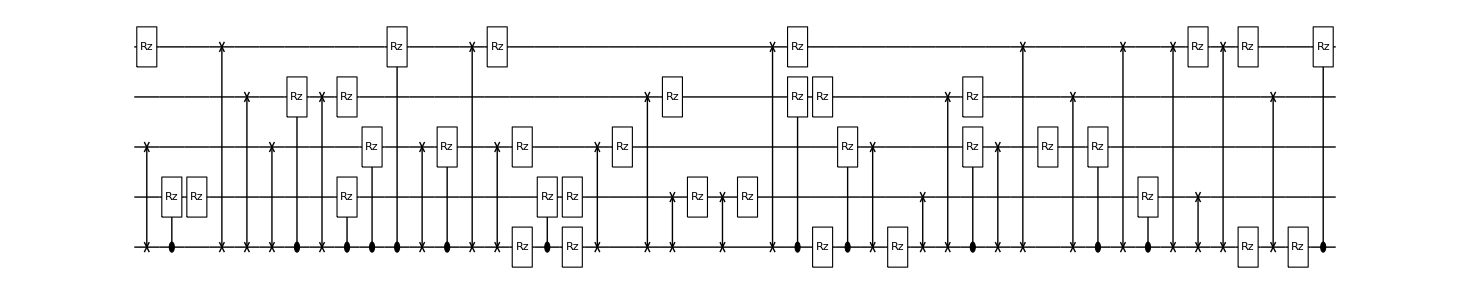

**** Compile @Tue 20 Dec 2022 22:17:35 τ=17.6; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 22:24:37 completed with ngates=46, cost=2.9393149334477897e-6, at eval=1593

Cycle 2@Tue 20 Dec 2022 22:28:03 adjust hyperparams, slowdown:True

@cycle3, pathetic result.

Cycle 3@Tue 20 Dec 2022 22:34:24 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=2.93931×10^-6

τ=17.8; δ=0.2; cost=2.93931×10^-6; ngates=46; runtime=18.4217 min

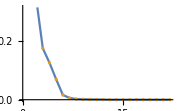

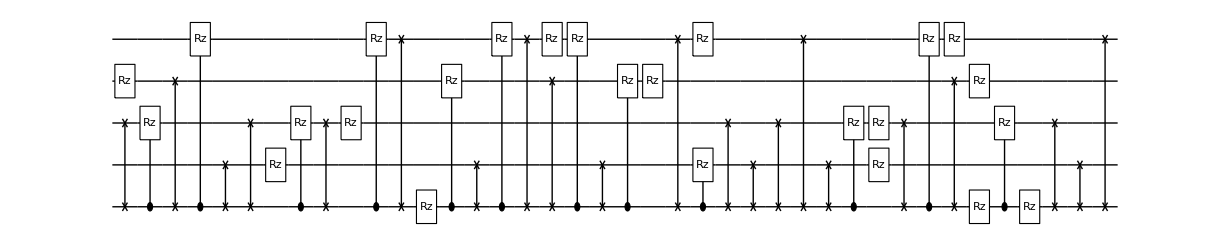

**** Compile @Tue 20 Dec 2022 22:36:07 τ=17.8; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 22:45:39 completed with ngates=42, cost=3.297279135505704e-6, at eval=2278

Cycle 2@Tue 20 Dec 2022 22:48:35 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 22:54:06 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=3.29728×10^-6

τ=18.; δ=0.2; cost=3.29728×10^-6; ngates=42; runtime=19.5049 min

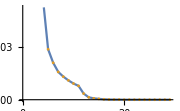

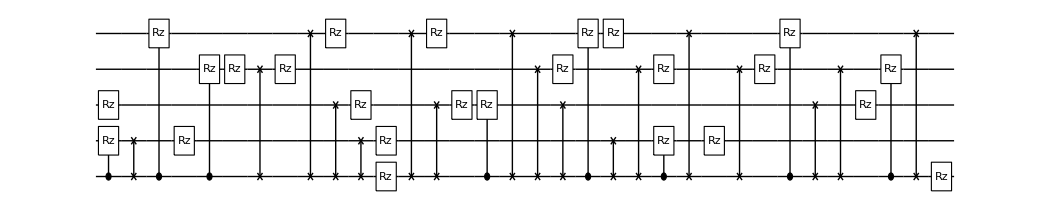

**** Compile @Tue 20 Dec 2022 22:55:44 τ=18.; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 23:01:34 completed with ngates=39, cost=0.000026928862676300902, at eval=1448

Cycle 2@Tue 20 Dec 2022 23:04:02 adjust hyperparams, slowdown:True

Cycle 3@Tue 20 Dec 2022 23:09:18 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000269289

τ=18.2; δ=0.2; cost=0.0000252851; ngates=39; runtime=14.3052 min

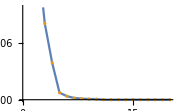

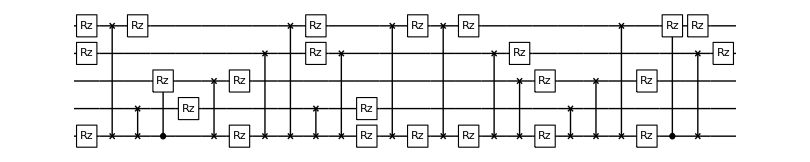

**** Compile @Tue 20 Dec 2022 23:10:10 τ=18.2; δ0.2 ****

Cycle 1@Tue 20 Dec 2022 23:16:13 completed with ngates=33, cost=0.0001911670682707145, at eval=1509

Cycle 2@Tue 20 Dec 2022 23:21:45 completed with ngates=34, cost=0.0000346233845627264, at eval=3137

Cycle 3@Tue 20 Dec 2022 23:24:24 adjust hyperparams, slowdown:True

Cycle 4@Tue 20 Dec 2022 23:35:02 completed with ngates=50, cost=5.258053460521772e-6, at eval=5385

Cycle 5@Tue 20 Dec 2022 23:42:12 adjust hyperparams, slowdown:True

τ=18.4; δ=0.2; cost=5.22644×10^-7; ngates=101; runtime=98.2007 min

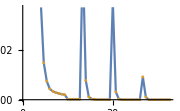

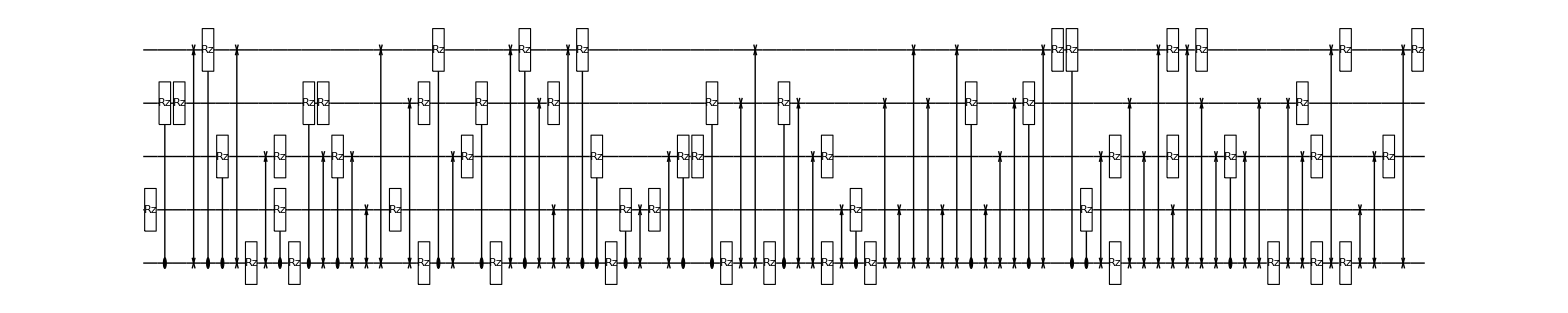

**** Compile @Wed 21 Dec 2022 00:48:30 τ=18.4; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 00:56:38 completed with ngates=49, cost=4.21250375459703e-6, at eval=1644

Cycle 2@Wed 21 Dec 2022 01:00:24 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 01:07:06 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=4.2125×10^-6

τ=18.6; δ=0.2; cost=2.75533×10^-6; ngates=49; runtime=22.1157 min

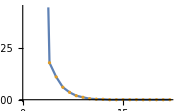

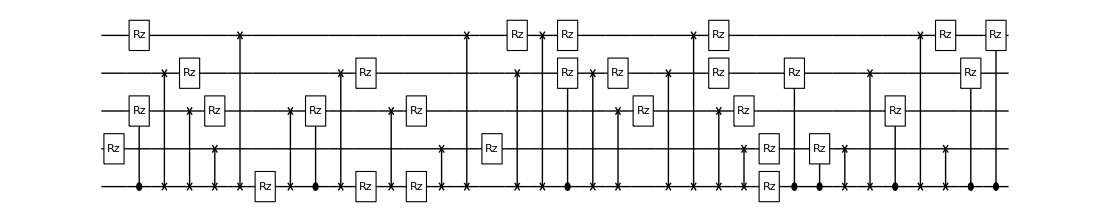

**** Compile @Wed 21 Dec 2022 01:10:43 τ=18.6; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 01:16:41 completed with ngates=41, cost=0.0002489202116254807, at eval=1470

Cycle 2@Wed 21 Dec 2022 01:22:25 completed with ngates=43, cost=0.00003656690444986399, at eval=2780

Cycle 3@Wed 21 Dec 2022 01:25:39 adjust hyperparams, slowdown:True

Cycle 4@Wed 21 Dec 2022 01:37:13 completed with ngates=50, cost=4.775076234975195e-6, at eval=4857

Cycle 5@Wed 21 Dec 2022 01:44:15 adjust hyperparams, slowdown:True

τ=18.8; δ=0.2; cost=6.28146×10^-7; ngates=76; runtime=79.3414 min

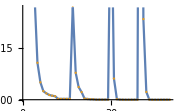

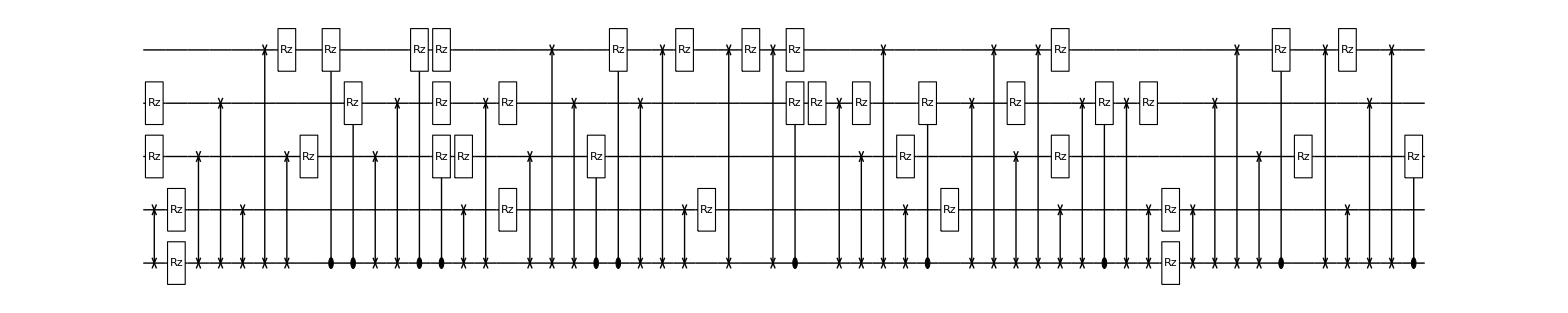

**** Compile @Wed 21 Dec 2022 02:30:11 τ=18.8; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 02:35:59 completed with ngates=36, cost=0.000031204765654213595, at eval=1486

Cycle 2@Wed 21 Dec 2022 02:38:34 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 02:48:58 completed with ngates=51, cost=2.2197618767538785e-6, at eval=3676

τ=19.; δ=0.2; cost=7.62015×10^-7; ngates=68; runtime=35.6558 min

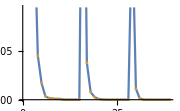

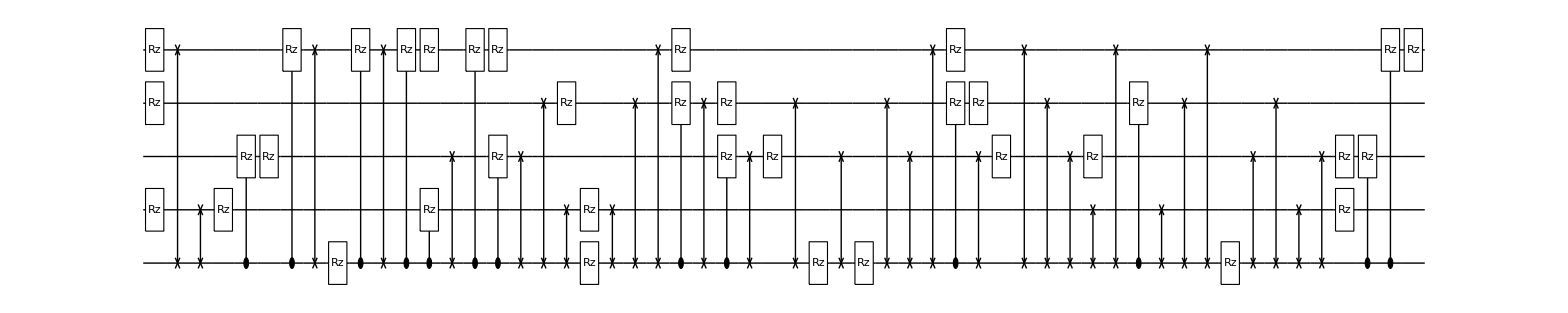

**** Compile @Wed 21 Dec 2022 03:05:56 τ=19.; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 03:11:27 completed with ngates=36, cost=0.0006810986745411363, at eval=1466

Cycle 2@Wed 21 Dec 2022 03:15:28 completed with ngates=31, cost=0.00008138086528208799, at eval=2684

Cycle 3@Wed 21 Dec 2022 03:21:34 completed with ngates=46, cost=0.000013239154413313692, at eval=4090

Cycle 4@Wed 21 Dec 2022 03:24:51 adjust hyperparams, slowdown:True

Cycle 5@Wed 21 Dec 2022 03:30:46 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000132392

τ=19.2; δ=0.2; cost=0.0000127245; ngates=46; runtime=26.0804 min

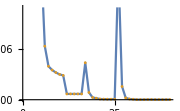

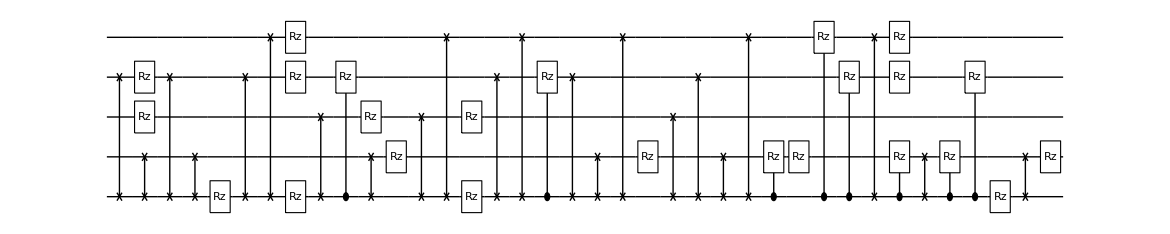

**** Compile @Wed 21 Dec 2022 03:32:08 τ=19.2; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 03:38:31 completed with ngates=40, cost=0.000043839253860866734, at eval=1915

Cycle 2@Wed 21 Dec 2022 03:40:54 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 03:50:03 completed with ngates=51, cost=0.000010627301050059046, at eval=4106

Cycle 4@Wed 21 Dec 2022 03:56:30 adjust hyperparams, slowdown:True

Cycle 5@Wed 21 Dec 2022 04:23:02 completed with ngates=59, cost=1.7337488152913139e-6, at eval=7443

τ=19.4; δ=0.2; cost=4.70243×10^-7; ngates=64; runtime=68.6648 min

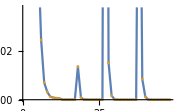

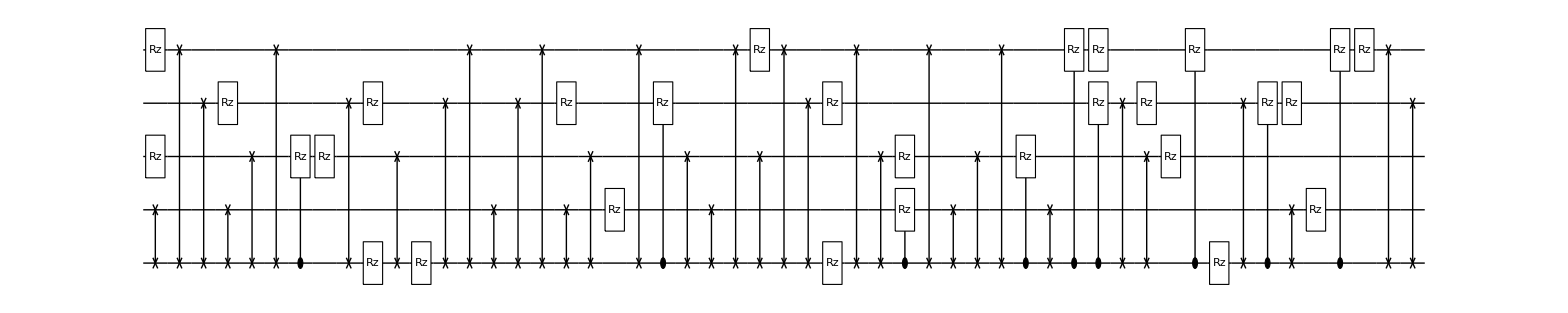

**** Compile @Wed 21 Dec 2022 04:40:54 τ=19.4; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 04:45:43 completed with ngates=34, cost=0.00003868514081284413, at eval=1439

Cycle 2@Wed 21 Dec 2022 04:47:49 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 04:58:40 completed with ngates=50, cost=3.2075097775585704e-6, at eval=4136

Cycle 4@Wed 21 Dec 2022 05:05:03 adjust hyperparams, slowdown:True

τ=19.6; δ=0.2; cost=4.09311×10^-7; ngates=60; runtime=44.9284 min

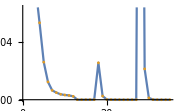

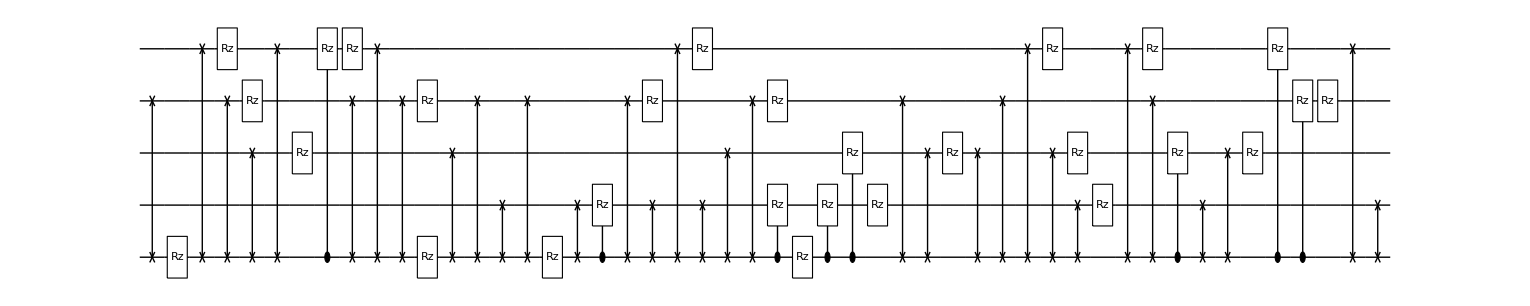

**** Compile @Wed 21 Dec 2022 05:25:56 τ=19.6; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 05:31:53 completed with ngates=42, cost=0.00001329732462740374, at eval=1613

Cycle 2@Wed 21 Dec 2022 05:34:32 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 05:39:37 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000132973

τ=19.8; δ=0.2; cost=0.0000132973; ngates=42; runtime=14.7068 min

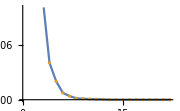

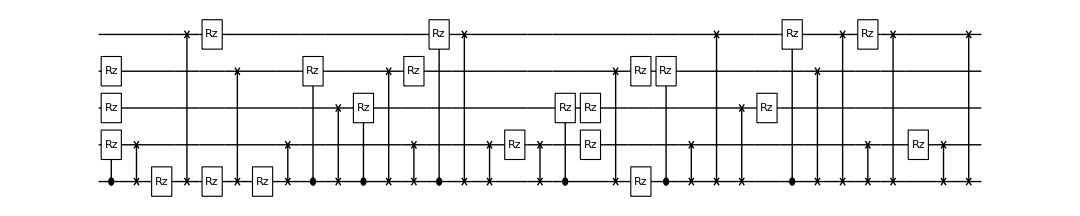

**** Compile @Wed 21 Dec 2022 05:40:45 τ=19.8; δ0.2 ****

Cycle 1@Wed 21 Dec 2022 05:46:02 completed with ngates=39, cost=0.000023673757867714862, at eval=1475

Cycle 2@Wed 21 Dec 2022 05:48:23 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 06:01:36 completed with ngates=58, cost=4.093763819823515e-6, at eval=4338

@cycle4, pathetic result.

Cycle 4@Wed 21 Dec 2022 06:08:46 adjust hyperparams, slowdown:True

τ=20.; δ=0.2; cost=3.81869×10^-7; ngates=65; runtime=62.1307 min

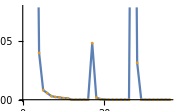

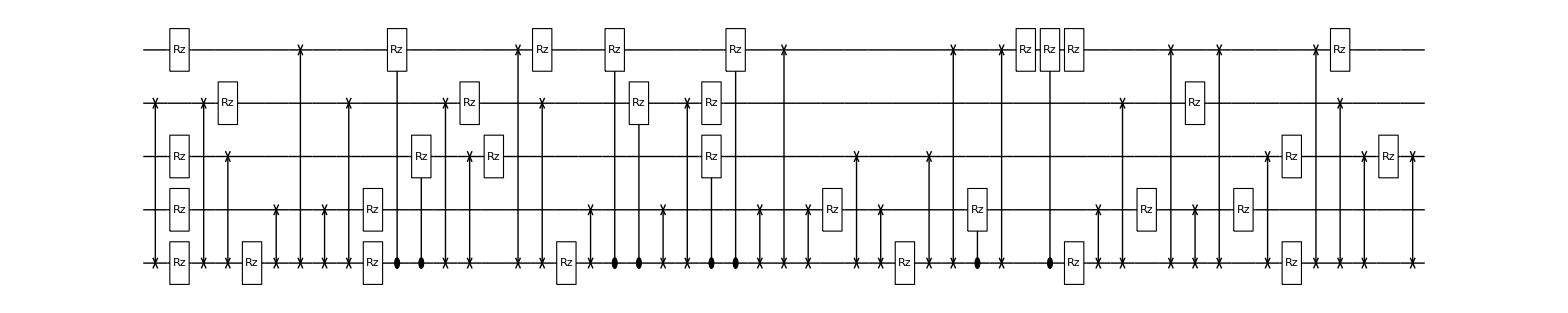

**** Compile @Wed 21 Dec 2022 06:42:59 τ=20.; δ3.5 ****

Cycle 1@Wed 21 Dec 2022 06:49:01 completed with ngates=47, cost=0.00001691278997073553, at eval=1607

Cycle 2@Wed 21 Dec 2022 06:51:54 adjust hyperparams, slowdown:True

Cycle 3@Wed 21 Dec 2022 06:57:35 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=0.0000169128

τ=23.5; δ=3.5; cost=0.0000144735; ngates=47; runtime=15.7432 min

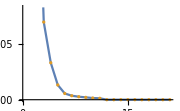

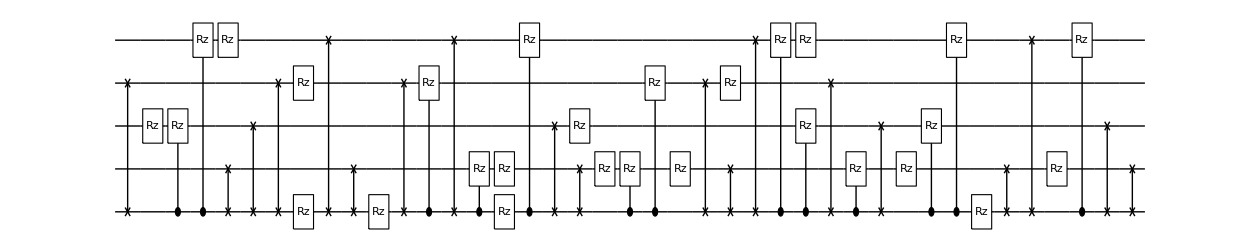

**** Compile @Wed 21 Dec 2022 06:58:50 τ=23.5; δ3.5 ****

Cycle 1@Wed 21 Dec 2022 07:04:55 completed with ngates=49, cost=0.00006742101682954971, at eval=1634

Cycle 2@Wed 21 Dec 2022 07:11:50 completed with ngates=46, cost=8.549529330714734e-6, at eval=3492

Cycle 3@Wed 21 Dec 2022 07:14:34 adjust hyperparams, slowdown:True

Cycle 4@Wed 21 Dec 2022 07:19:46 adjust hyperparams, slowdown:True

pruning exceeds the maxcost: 1.×10^-6; cost=8.54953×10^-6

τ=27.; δ=3.5; cost=8.54953×10^-6; ngates=46; runtime=21.9683 min

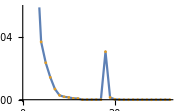

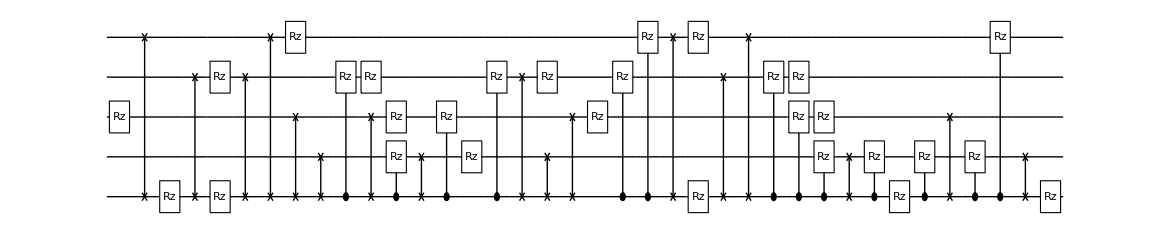

```mathematica
τ=τs[[32]];
bcscompilecss2={};
Table[
Print["**** Compile @",DateString[]," τ=",τ, "; δ",δ," ****"];
hbcsmat=Chop@MatrixExp[-ⅈ *δ*CalcPauliStringMatrix[HBCS[5,ϵ,τ]]]; 
DestroyAllQuregs[];
τ+=δ;
conf=DefaultConfig[5,{1,2,4,8,16}];
res=CJRecompile[5,hbcsmat,conf];
AppendTo[bcscompilecss2,{τ,δ,res}];

DumpSave["bcscompilecss2.mx",bcscompilecss2];
{time,Ecur,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elimmerge,elimbfsmall,elimmetov,elimbf}=res;
Print["τ=",τ, "; δ=",δ,"; cost=",Ecur,"; ngates=",Length@ansatz,"; runtime=",time];
Print@ListPlot[{Elist,Elist},Joined->{True,False},ImageSize->Small];
Print@DrawCircuit[ansatz/.CustomGatesDraw,5];
,{δ,δτ[[33;;]]}];
```

```mathematica
rexactot2<<rexactot2.mx
```

Null rexactot2

The matrixExp vs compiled

```mathematica
(*initialisation*)
{ψexact,ψinitexact}=CreateQuregs[5,2];
hbcs0=HBCS[5,ϵ,0];
{eigval,eigvec}=Eigensystem[CalcPauliStringMatrix@hbcs0];
Ordering[eigval,1];
initv=eigvec[[First@Ordering[eigval,1]]];
SetQuregMatrix[ψinitexact,initv];
```

```mathematica
CloneQureg[ψexact,ψinitexact];
rexactcomp={{0,1}};
Table[
{τ,δ,res}=comp;
ApplyCircuit[ψexact,res[[4]]/.CustomGatesDefinitions/.res[[5]]];
AppendTo[rexactcomp,{τ,CalcFidelity[ψexact,ψinitexact]}]
,{comp, bcscompilecss2}];
```

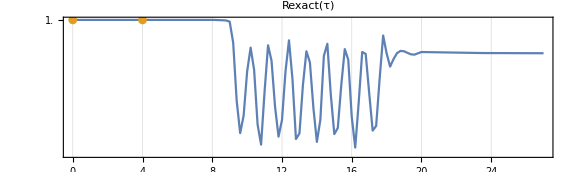

```mathematica
ListPlot[{rexactot2,rexactcomp},Joined->{True,False},PlotTheme->"Detailed",AspectRatio->0.3,PlotLabel->"Rexact(τ)",ImageSize->Large,FrameTicks->{{Range[1,1.55,0.05],None},{Automatic,None}}]
```